Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 1. Grafica e teoria dei numeri

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 1.1 (Approssimazione di funzione con il suo sviluppo di Taylor).

### Testo dell’esercizio

Come sono approssimate le funzioni sin(x) e 1/(1+x^2) dai loro polinomi di Taylor di ordine crescente?

### Svolgimento

Dopo un tentativo andato molto molto male di sfruttare lo sviluppo di Taylor scritto da me invece che il built-in, ricomincio.

Il mio obiettivo è di plottare su una griglia dei grafici con passo che aumenta tra le righe di f(x) contro il suo sviluppo in serie di Taylor (in 0), cominciamo dicendo

```mathematica
g[x_]:= 1/(1+x^2)
```

Ora necessito che lo step tra i grafici di una riga sia n quindi automatizzo la creazione delle righe per una funzione generica in un intervallo fissato [-10,10] per limitare le variabili. diamo anche una lunghezza di 4 
fissata alle righe e ricordandoci di quale ordine stiamo facendo il grafico

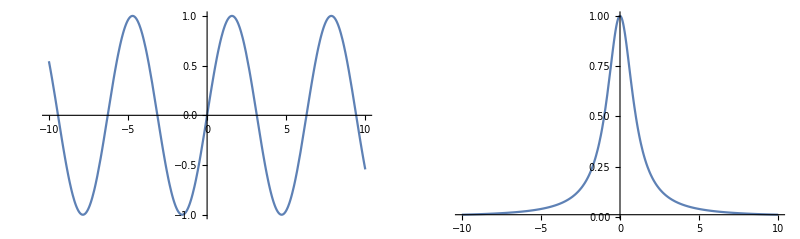

```mathematica
GraphicsRow[{Plot[Sin[x],{x,-10,10}],Plot[g[x],{x,-10,10},PlotRange->Full]}]
```

Possiamo notare che possiamo tenere un PlotRange tra -1 ed 1 senza separarle , per sicurezza facciamo 1.5 valà

```mathematica
Rows[f_,x_,start_,step_]:=Table[Plot[{f[x] , Series[f[x],{x,0,k}]//Normal//Evaluate},{x,-10,10},PlotLabel->k,PlotRange->{-1.5,1.5}],{k,start,start+4 step,step}]
```

La funzione crea una table con il grafico di f(x) e quello della sua serie di Taylor al k-esimo ordine con k che varia, facendo 4 grafici per riga con step fissato

Creiamo una funzione che dia una matrice fatta di “Rows” dove lo step incrementi col numero di righe. ciò crea un problema nel calcolare con cosa far cominciare le righe.

```mathematica
Gridd[f_,x_,n_]:= Table[Rows[f,x,st[k],k],{k,1,n}]
```

lo start della riga 1 è 1, lo start della riga 2 è (1 + 4step(1)+step(1)), lo start della riga 3 è (start della riga 2 + 4step(2)+step(2)) viene in mente di definire ricorsivamente st[k], ricordandoci che step(k) = k per definizione

```mathematica
st[k_]:= st[k-1]+ 5k
```

```mathematica
st[1] := 1
```

Plottiamo e mettiamo in una tabella

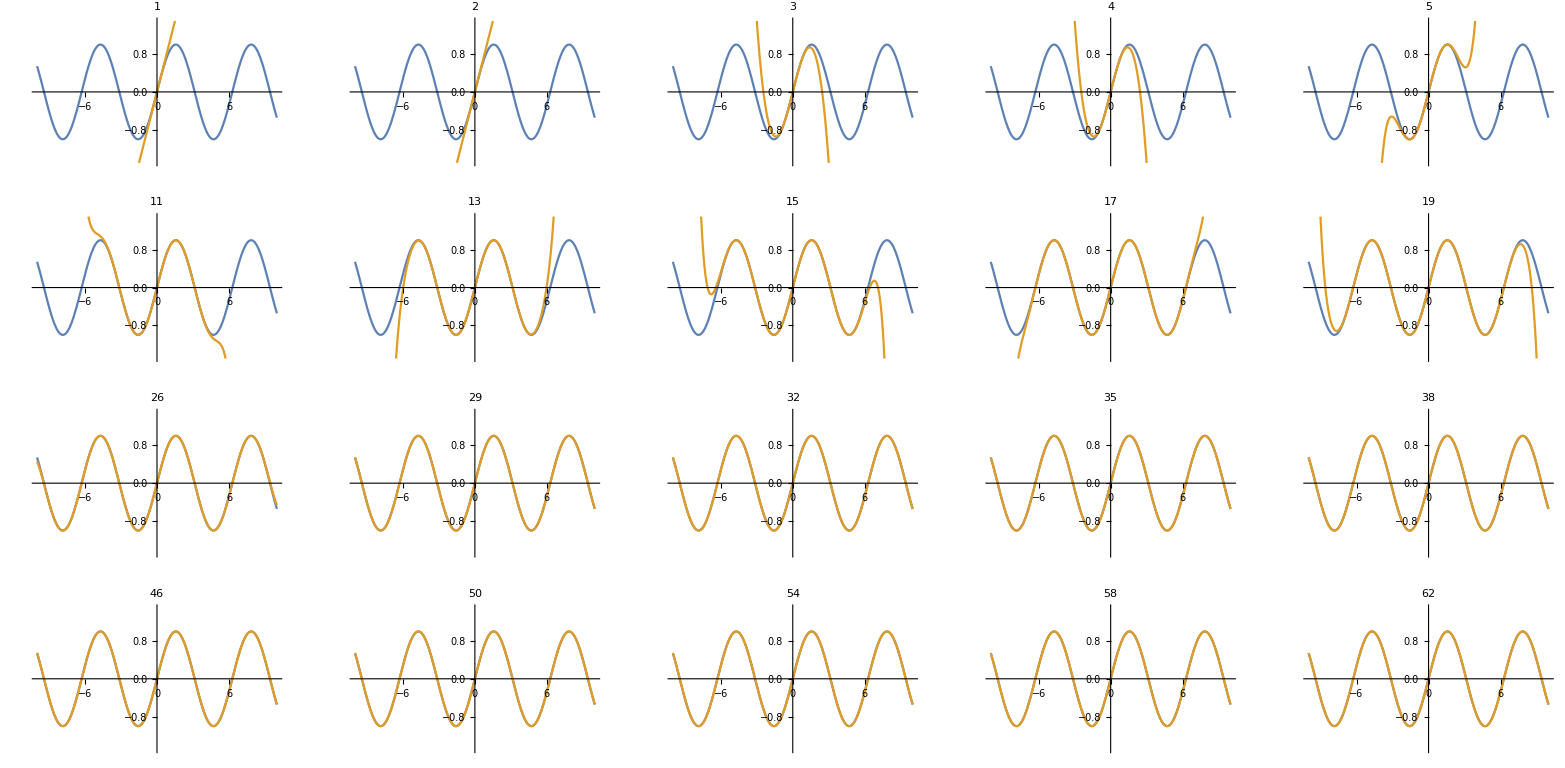

```mathematica
GraphicsGrid[Gridd[Sin,x,4],ImageSize->Full]
```

Proviamo a fare lo stesso con g

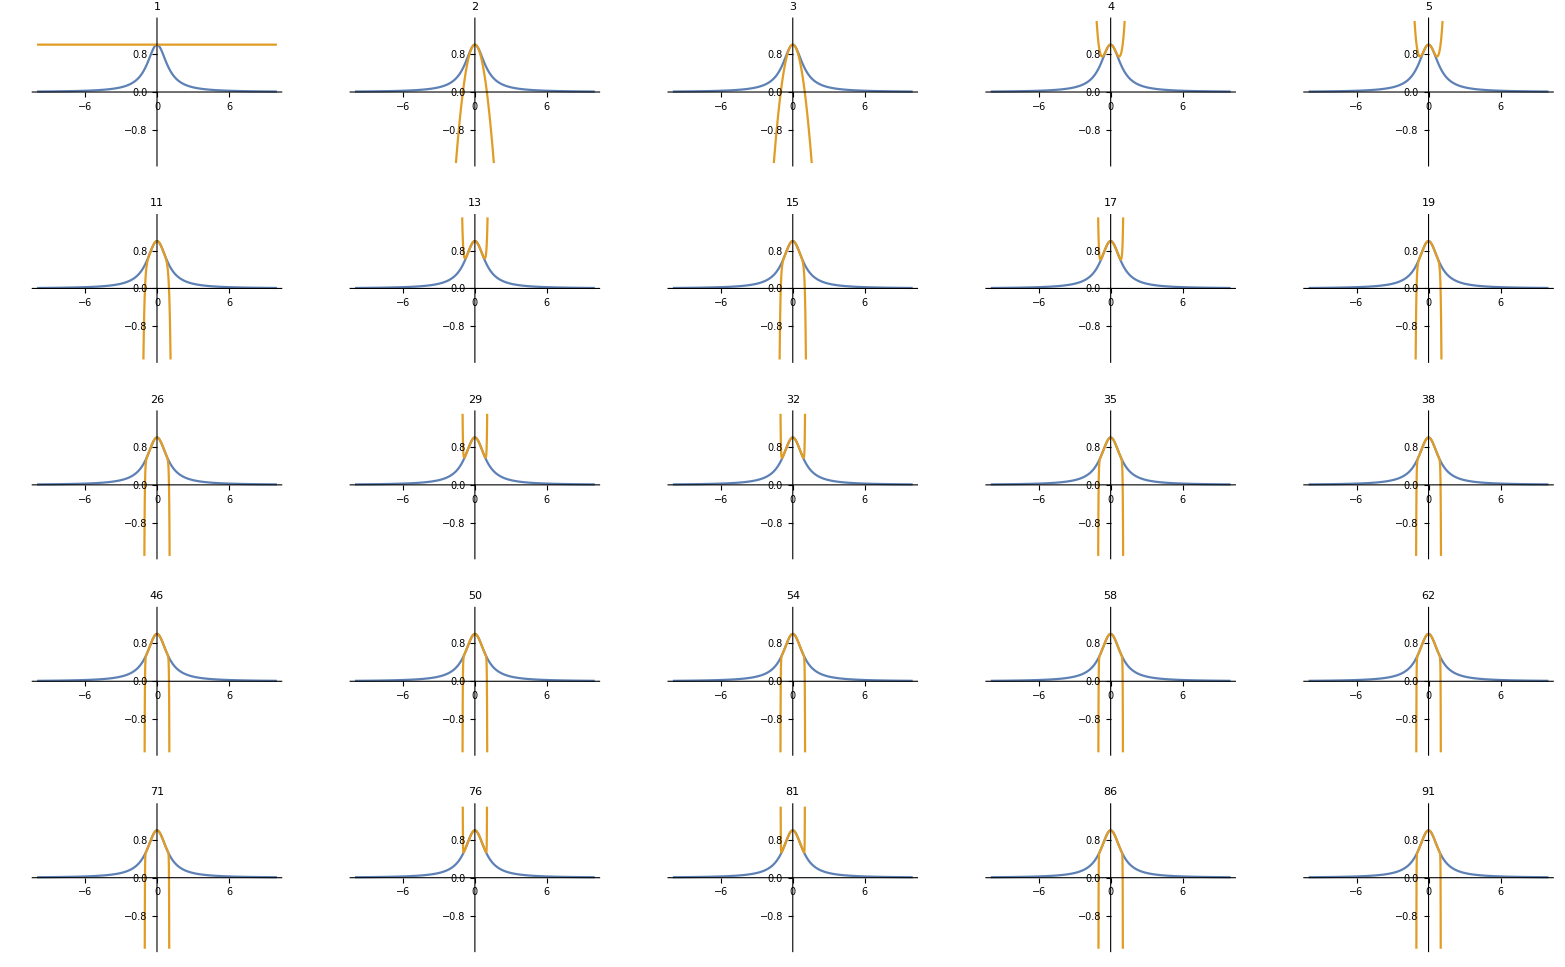

```mathematica
GraphicsGrid[Gridd[g,x,5],ImageSize->Full]
```

Si notano subito spiccate differenze sulla convergenza tra Sin(x) e 1/(1+x^2), la serie di Sin(x), pur essendo entrambe analitiche. 
Lo sviluppo di Sin(x) si “appiccica” alla funzione nell’intervallo [-10,10] in meno di 30 iterazioni, quello di 1/(1+x^2) in 100 non è arrivato a metà
Mi vien da chiedermi quanto sia veloce l’approssimazione, posso provare a farlo plottando n sul il primo x>0 per cui lo sviluppo di ordine n è diverso dalla funzione (entrambe le funzioni hanno simmetrie comode)
scritto matematicamente F(n) = inf(x>0 : |f(x)-s.taylor ord. n f(x)|>0 ), scritto mathematicamente

```mathematica
dst[f_,x_,n_] := Abs[f[x]-Evaluate@Normal[Series[f[x],{x,0,n}]]]
```

Forse c’è un metodo migliore ma si può risolvere numericamente mettendogli un numero “piccolo”>0, forse c’è un metodo migliore

```mathematica
ConvSin=FindRoot[dst[Sin,x,#]==0.01,{x,#-2}]&
```

```mathematica
Convg=FindRoot[dst[g,x,#]==0.01,{x,#/55}]&
```

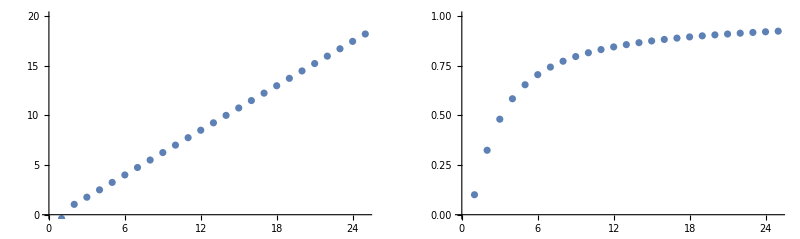

```mathematica
GraphicsRow [{ListPlot[x/.ConvSin/@Range[1,50,2],PlotRange->{0,20}],ListPlot[x/.Convg/@Range[1,50,2],PlotRange->{0,1}]}]
```

Sembra una convergenza lineare la prima e logaritmica la seconda.
possiamo vedere come nel medesimo numero di passi il primo sviluppo di Taylor stia “incollato” alla funzione fino a circa x = 20, il secondo circa a x = 1

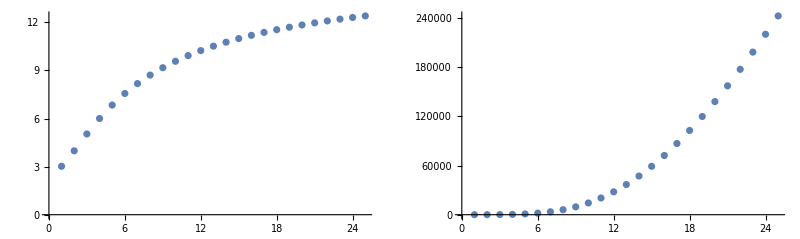

```mathematica
GraphicsRow[{ListPlot[Exp@Exp[x/.Convg/@Range[1,50,2]]],ListPlot[Exp@Exp@Exp[x/.Convg/@Range[1,50,2]]]}]
```

Tuttavia se plottiamo e^(f(x)) è concava (=> sublineare), così come e^(e^(f(x))), tuttavia e^(e^(e^(f(x))))diventa convessa (=> superlineare), credo si può concludere che la convergenza dell’approssimazione di taylor di 1/(1+x^2) alla funzione sia compresa tra log(log(x)) e log(log(log(x)))